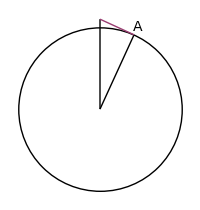

```mathematica
eps=.1;
h = Sqrt[(1+eps)^2-1];
b=((1+eps)^2-1)/(1+eps);
c=Sqrt[h^2-b^2];
pt={c, 1+eps-b};

Graphics[{
Circle[],
Line[{{0,0}, {0,1+eps}}],
Line[{{0,0}, pt}],
Text[Style["A", 14, Italic], (1+eps)*pt],
Thick,ColorData[1,2],Line[{{0,1+eps}, pt}]
},
ImageSize->200,
Axes->None]
```